```mathematica
V0 = 1;
a = 1;
m = 1;
hbar = 1;
term = (V0^2)/(2*en*(en - V0))*sin[√(2*m*en)/hbar *a];
T = 1/(term + 1);
Plot[Evaluate[T], {en, 0, 10}]
```

{{phi→InterpolatingFunction[…]}}

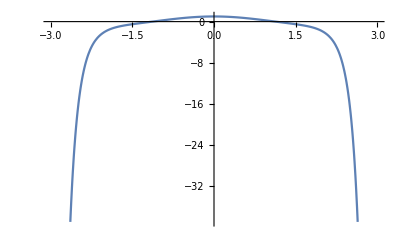

```mathematica
energy = 1;
sol = NDSolve[{-phi''[z] + z^4*phi[z] == epsilon * phi[z], phi[0]==1, phi'[0]==0}, phi, {z, -3, 3}]
Plot[Evaluate[phi[z] /.%], {z, -3, 3}]
```

```mathematica
energy = 2;
NDSolve[{-D[D[phi[z], z], z] + z^4 * phi[z] == epsilon*phi[z], phi[0]==1, phi'[0]==0}, phi[z], {z, -3, 3}]
Plot[Evaluate[phi[z] /. %], {z, -3, 3}]
```

{{phi[z]→InterpolatingFunction[…][z]}}

-Graphics-

```mathematica
e1= 28.0;
e2 = 39.0;
precision = 0.000001;
While[e2 - e1 > precision,
avg = (e1 + e2)/2;
sol = NDSolve[{-phi''[z] + z^4*phi[z] == avg*phi[z], phi[0]==1, phi'[0]==0}, phi, {z, -4, 4}];
If[Part[phi[4] /. sol, 1] > 0, e1 = avg];
If[Part[phi[4] /. sol, 1] < 0, e2 = avg];
]
NumberForm[e1, 7]
NumberForm[e2, 7]
```

37.923

37.923